```mathematica
updateState::usage = "Updates CA loop state based on rule";
updateState[rule_,state_]:=(
 CellularAutomaton[rule,state](*Single evolution of rule*)
)

getReading::usage = "Measures the state of a given index";
getReading[state_,readindex_]:=(
state[[readindex]]
)

getCandidates::usage = "Creates all possible candidate states that can be represented with a given number of bits";
getCandidates[data_]:=(
Tuples[{0,1},Dimensions[data]])

eliminateCandidates::usage = " Eliminates candidates that do not agree with the lates reading";
eliminateCandidates[candidates_,readindex_,reading_]:=(
Select[candidates,getReading[#,readindex]==reading&]
)


updateAllCandidates::usage = "Updates all candidate states";
updateAllCandidates[rule_,candidates_]:=(
updateState[rule,#1]&/@candidates
)

stepDecoder::usage = "Does a single step of the Decoder";
stepDecoder[rule_,candidates_,readindex_,reading_]:=(
updatedcandidates = updateAllCandidates[rule,candidates];
validcandidates = eliminateCandidates[updatedcandidates,readindex,reading])

encodeMasterState::usage = "Encodes data by reading a column of CA";
encodeMasterState[rule_,masterstate_,readindex_,nupdates_]:=(
CellularAutomaton[rule,masterstate,nupdates][[;;,readindex]])

Decode::usage = "Decodes the data, should not technically take masterstate as argument";
Decode[rule_,encodedsequence_,masterstate_,readindex_]:=(
candidates = getCandidates[masterstate];
n =1;
candidates = eliminateCandidates[candidates,readindex,encodedsequence[[n]]] ;(*Edge case*)
n=n+1;
While[Length[candidates]>1,
candidates = stepDecoder[rule,candidates,readindex,encodedsequence[[n]]];
(*Print[Length[candidates]];*)
n=n+1];
n)
```

```mathematica
rule = 30 (*RandomInteger[200]*);
datasize = 10;
readindex = 6;
ParallelDo[
masterstate= RandomInteger[{0,1},datasize];
readindex=RandomInteger[{1,datasize}];
encodedsequence = encodeMasterState[rule,masterstate,readindex,datasize*2];
Print[Decode[rule,encodedsequence,masterstate,readindex]],6 ]
```

9

12

10

11

13

15

```mathematica
|
```

```mathematica
rule = 30 (*RandomInteger[200]*);
datasize = 5;
readindex = 6;
masterstate= RandomInteger[{0,1},datasize];
readindex=RandomInteger[{1,datasize}];
encodedsequence = encodeMasterState[rule,masterstate,readindex,datasize*10];
Print[Decode[rule,encodedsequence,masterstate,readindex]]
```

Part::partw: Part 12 of {0,1,0,1,0,1,0,1,1,0,1} does not exist.

Part::partw: Part 13 of {0,1,0,1,0,1,0,1,1,0,1} does not exist.

Part::partw: Part 14 of {0,1,0,1,0,1,0,1,1,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1,1,1,0,1},{0,0,0,0,1},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1}}

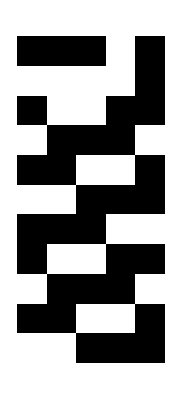

{1,0,1,0,1,0,1,1,0,1,0}

```mathematica
read = CellularAutomaton[rule,masterstate,10]
ArrayPlot[read]
read[[;;,1]]
```

```mathematica
encodeMasterState[rule,masterstate,measureindex,10]
```

{1,0,1,0,0,0,1,1,1,1,0}